```mathematica
generateRandomHermitianMatrix[n_]:=Module[{A,randomMatrix},randomMatrix=RandomComplex[NormalDistribution[0,1],{n,n}];
A=(randomMatrix+ConjugateTranspose[randomMatrix])/2;
A]
```

```mathematica
m=generateRandomHermitianMatrix[1000];
```

```mathematica
Mean[Differences[Sort[Eigenvalues[m]]]]
```

0.088986

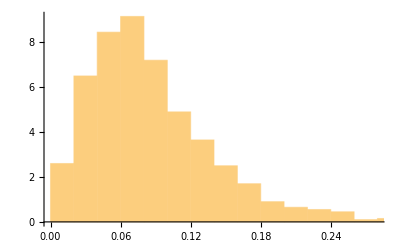

```mathematica
Histogram[Differences[Sort[Eigenvalues[m]]],Automatic,"PDF"]
```

```mathematica
eigValsM=RandomReal[{0,1},1000];
```

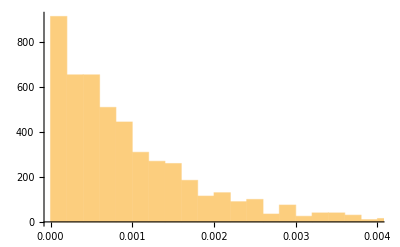

```mathematica
Histogram[Differences[Sort[eigValsM]],Automatic,"PDF"]
```

```mathematica
eigVecsM=RandomReal[{0,1},{1000,1000}];
```

```mathematica
M=Transpose[eigVecsM].DiagonalMatrix[eigValsM].Inverse[Transpose[eigVecsM]];
```

```mathematica
MatrixRank[Transpose[eigVecsM]]
```

1000